#### Preamble

```mathematica
ClearAll@@{$Context<>"*"}
SetDirectory[NotebookDirectory[]]
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; 
StartScheduledTask[saveTask] (*Saves nb each 15 minutes*) ;

<<"MaTeX`"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Maxima_Minima.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optics_Mie.wls"
<<"~/Documentos/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"
```

/home/juanathan/Documentos/MSc_Thesis/3-FEM-Calc

```mathematica
fs=9;

texStyle:={FontFamily->"Latin Modern Roman",FontSize->fs,Black};
graphsOpts:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->ColorData[3]}
graphsOptsDash:={Mesh->Full,BaseStyle->texStyle,Frame->True,FrameStyle->Black,ImageSize->215,PlotStyle->Table[Directive[Dashed,ColorData[3,i]],{i,10}]}

graphsOptsPolar:={Mesh->Full,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,PlotStyle->ColorData[3],Frame->False,PolarGridLines->Automatic,Joined->True}
```

## Single Particle - Supported NP

```mathematica
FileNames["*.csv","Single particle_Supported",Infinity];
data= Drop[Import[#,"Data"],5]&/@%;
TableForm[%%]
rad =12.5 (*nm*);
```

Single particle_Supported/1-Abs-Sca_th_c/AbsS_theta_c.csv
Single particle_Supported/1-Abs-Sca_th_c/ScaS_theta_c.csv
Single particle_Supported/2-Abs-Sca_th_i/AbsP_theta_i.csv
Single particle_Supported/2-Abs-Sca_th_i/AbsS_theta_i.csv
Single particle_Supported/2-Abs-Sca_th_i/ScaP_theta_i.csv
Single particle_Supported/2-Abs-Sca_th_i/ScaS_theta_i.csv
Single particle_Supported/3-Far Field 2D/Efar_pPol_normalX_500nm.csv
Single particle_Supported/3-Far Field 2D/Efar_pPol_normalY_500nm.csv
Single particle_Supported/3-Far Field 2D/Efar_sPol_normalX_500nm.csv
Single particle_Supported/3-Far Field 2D/Efar_sPol_normalY_500nm.csv
Single particle_Supported/4-Normal incidence/Efar_pPol_theta_i0_normalX.csv
Single particle_Supported/4-Normal incidence/Efar_pPol_theta_i0_normalY.csv
Single particle_Supported/4-Normal incidence/Efar_sPol_theta_i0_normalX.csv
Single particle_Supported/4-Normal incidence/Efar_sPol_theta_i0_normalY.csv
Single particle_Supported/4-Normal incidence/Q_normalIncidence_p.csv
Single particle_Supported/4-Normal incidence/Q_normalIncidence_s.csv
Single particle_Supported/5-external_all.csv
Single particle_Supported/6-internal_all.csv

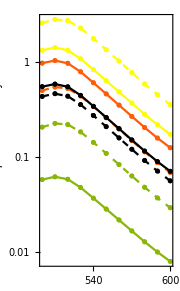
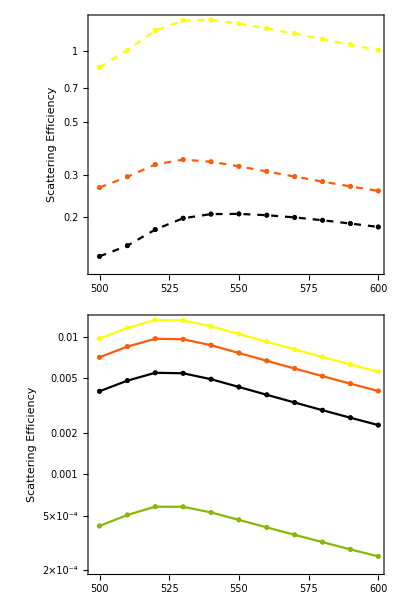

```mathematica
(*Internal Incicdence\n12.5 nm-AuNP@Air/BK7*)
absAngle=Transpose@(data[[3;;4,;;,{2,#}]]&/@Range[3,6]) (*absorption - 15, 38, 42, 80, P/S*);
scaAngle = Transpose@(data[[5;;6,;;,{2,#}]]&/@Range[3,6]) (*absorption - 15, 38, 42, 80, P/S*);
legend = SwatchLegend[ColorData[3,#]&/@Range[4],Style[#,texStyle]&/@({15,38,42,80}Degree),LegendLayout->"Row"]
plot = {0,0};

plot[[1]] = MapThread[ListLinePlot[#1,ScalingFunctions->"Log",ImageSize->180,Evaluate[#2],AspectRatio->GoldenRatio,PlotRange->Full,
Axes->False, FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Absorption Efficiency"}]&,
{absAngle,{graphsOptsDash,graphsOpts}}];
plot[[1]] =Show[plot[[1]] ,PlotRange->Full];

plot[[2]] =MapThread[ListLinePlot[#1,ImageSize->180,ScalingFunctions->"Log",Evaluate[#2],
FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Scattering Efficiency"}]&,
{scaAngle,{graphsOptsDash,graphsOpts}}];

Row[{#1,Column[#2]}]&@@plot
(*
Export[FileNameJoin[{"Single particle_Supported","Efficiencies_Angles.svg"}],Grid[{%%,%}]]*)
```

```mathematica
thTiks=Table[{i*Pi/180.,
Which[i≤90,(90-i)Degree,
i<= 180,""(*Mod[i,90]*),
i< 270,(90-Mod[i,90])Degree,
True, Mod[i,90]Degree
]},{i,0,360,15}]
```

{{0.,90 °},{0.261799,75 °},{0.523599,60 °},{0.785398,45 °},{1.0472,30 °},{1.309,15 °},{1.5708,0},{1.8326,},{2.0944,},{2.35619,},{2.61799,},{2.87979,},{3.14159,},{3.40339,75 °},{3.66519,60 °},{3.92699,45 °},{4.18879,30 °},{4.45059,15 °},{4.71239,0},{4.97419,15 °},{5.23599,30 °},{5.49779,45 °},{5.75959,60 °},{6.02139,75 °},{6.28319,0}}

```mathematica
graphsOptsPolar:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[PointSize[.015],ColorData[3,i]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
graphsOptsPolarDashed:={Mesh->30,BaseStyle->texStyle,PolarAxes->True,FrameStyle->Black,ImageSize->215,
	PlotStyle->Table[Directive[Dashed,PointSize[.015],ColorData[3,i]],{i,10}],PolarGridLines->Automatic,Joined->True,GridLinesStyle->Directive[Gray,Opacity[.1]],
	PolarAxesOrigin->{{Left,Up},Automatic}}
```

```mathematica
arrows2 =MapThread[{ColorData[3,#],Arrow[-{2{Cos[#2],Sin[#2]},.5{Cos[#2],Sin[#2]}}],}&,{Range[4],{15.,38.,42.,80.}Degree}];

arrows3 =MapThread[{ColorData[3,#],Arrow[-{3{Cos[#2],Sin[#2]},.5{Cos[#2],Sin[#2]}}]}&,{Range[4],{15.,38.,42.,80.}Degree}];
arrows1 =MapThread[{ColorData[3,#],Arrow[-{1.25{Cos[#2],Sin[#2]},.25{Cos[#2],Sin[#2]}}]}&,{Range[4],{15.,38.,42.,80.}Degree}];
```

```mathematica
scatteredField = Partition[#,101]&/@(Drop[#,3]&/@data[[7;;10]]) ;

MapThread[
ListPolarPlot[#1/.{theta_,radius_}-> {theta+Pi/2.,#2*radius},PlotRange->#3,
Evaluate[#5],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0},#3,{0,-Pi}],LightYellow,Disk[{0,#3}/3.5,#3/3.5]},
Epilog->#4
]&,
{scatteredField,{1*^7,1*^7,1*^9,1*^9},{2.7,4,1.7,1.7}(*{2.25,3.5,1.5,1.5}*),{arrows2,arrows3,arrows1,arrows1},{graphsOptsPolarDashed,graphsOptsPolarDashed,graphsOptsPolar,graphsOptsPolar}}]
MapIndexed[Export[
FileNameJoin[{"SingleParticle_Supported","Scattered_"<>ToString[#2[[1]]]<>".svg"}],
#1]&,%]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{SingleParticle_Supported/Scattered_1.svg,SingleParticle_Supported/Scattered_2.svg,SingleParticle_Supported/Scattered_3.svg,SingleParticle_Supported/Scattered_4.svg}

```mathematica
arrows ={Black,Arrow[-{{Cos[#],Sin[#]},.025{Cos[#],Sin[#]}}]&[Pi/2]};
```

```mathematica
scatteredFieldNormal = Partition[#,101]&/@(Drop[#,3]&/@data[[11;;14]]) ;
MapThread[
ListPolarPlot[#1/.{theta_,radius_}-> {theta+Pi/2.,1*^9*radius},PlotRange->#2,
Evaluate[#3],
PolarTicks->{thTiks[[;;-2]],Automatic},
Prolog->{LightBlue,Disk[{0,0},#2,{0,-Pi}],LightYellow,Disk[{0,#2}/3.5,#2/3.5]},
Epilog->arrows
]&,
{scatteredFieldNormal,Table[1.35,{4}],{graphsOptsPolarDashed,graphsOptsPolarDashed,graphsOptsPolar,graphsOptsPolar}}]
(*MapIndexed[Export[
FileNameJoin[{"SingleParticle_Supported","Scattered_"<>ToString[#2[[1]]]<>".svg"}],
#1]&,%]*)
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

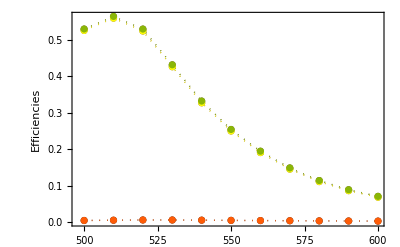

Single particle_Supported/Q_normal.svg

```mathematica
(*Normal incidence (p,s)*)
ListPlot[#,BaseStyle->texStyle,PlotStyle->Table[Directive[Thick,Dotted,ColorData[4,i]],{i,2,4}],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],Joined->True,Mesh->True,
FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"}
]&@(data[[15,;;,{2,#}]]&/@Range[3,5]);

ListPlot[#,BaseStyle->texStyle,PlotStyle->Table[Directive[Thick,Dotted,ColorData[3,i]],{i,2,4}],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],Joined->True,Mesh->True,
FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"}
]&@(data[[16,;;,{2,#}]]&/@Range[3,5]);

Show[{%%,%}]
Export[FileNameJoin[{"Single particle_Supported","Q_normal.svg"}],%]
```

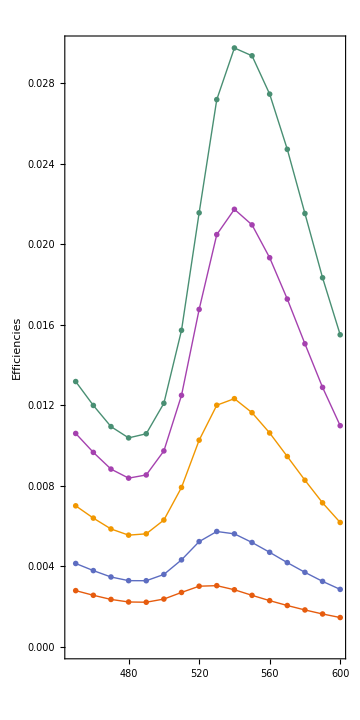
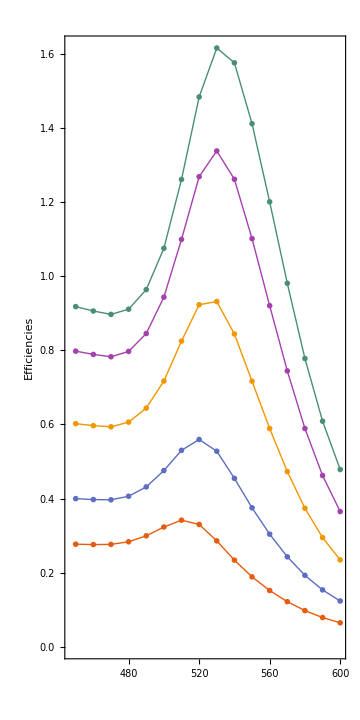
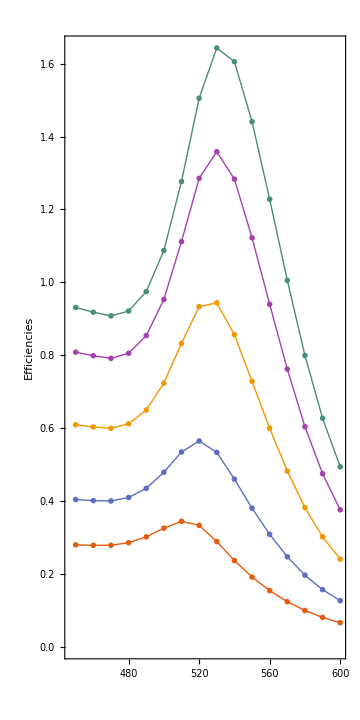

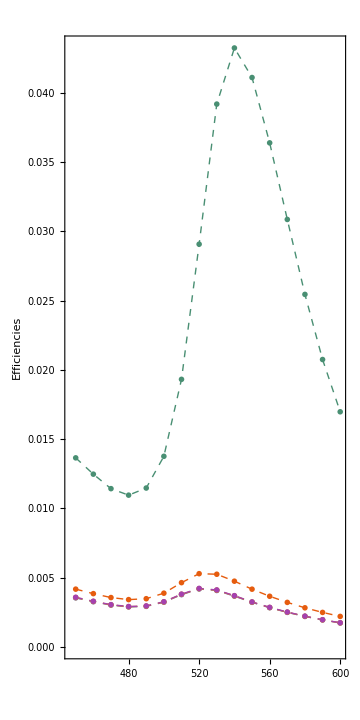
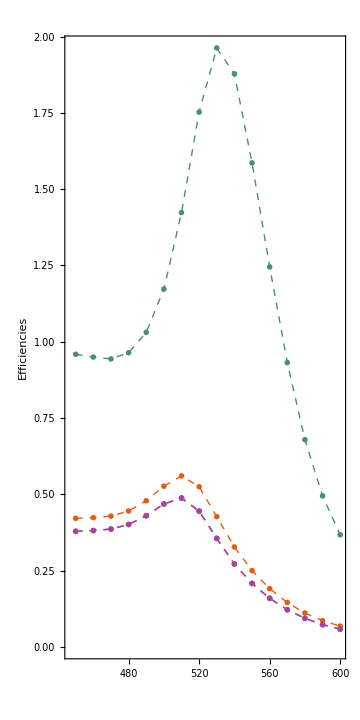
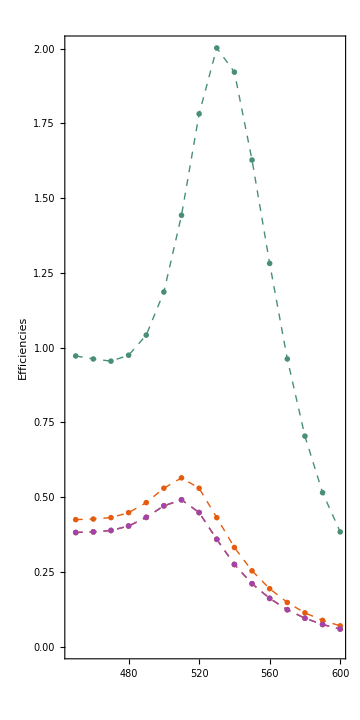

```mathematica
(*ListLinePlot[#,PlotStyle->Directive[Thick],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->2]&/@ (data[[17,;;,{1,#}]]&/@Range[#,3*5+1,3]&/@Range[2,4])*)

ListLinePlot[#,PlotStyle->Directive[Thick],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->2]&/@{scaData,absData,extData}
(*MapThread[Show,{%,%%}]*)


ListLinePlot[#,PlotStyle->Directive[Thick,Dashed],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->2,PlotRange->All]&/@ Reverse/@(data[[18,;;,{1,#}]]&/@Range[#,3*5+1,3]&/@Range[2,4])

(*Export[FileNameJoin[{"Single particle_Supported","Q_int_ext.svg"}],Row[%]]*)
```

## Incrusted Cases

```mathematica
FileNames[FileNameJoin[{"Incrusted","*.csv"}]]
data = Drop[ Import[#,"Data"],6]& /@%;
```

{Incrusted/IlluminatedAir.csv,Incrusted/IlluminatedBK7.csv}

```mathematica
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
```

#### Data

```mathematica
{fromAir,fromBK7} = Transpose@Table[{data[[2,;;,{1,#}]]& /@ Range[i,Length[data[[1,1]] ], 3],Reverse@(data[[1,;;,{1,#}]]& /@Range[i,Length[data[[1,1]] ], 3])},{i,2,4}];
```

```mathematica
nAuSize[λ_,a_]:=Sqrt[εAuFuncSpline[λ]-(1-λ/λp^2*1/(1/λ + I/γ))+(1-λ/λp^2*1/(1/λ + I(1/γ+1/γsize)))/.{λp->142.609,γ->14966.2,γsize->(a *2 π c)/(1.4*^15)}(*Values for Au*)]
sca = Table[{λ,scaQ[{1.,nAuSize[λ,12.5]},λ,12.5],scaQ[{1.5,nAuSize[λ,12.5]},λ,12.5]},{λ, 450,600}];
sca = Transpose[sca /.{x_,y_,z_}-> {{x,y},{x,z}}];

ext = Table[{λ,extQ[{1.,nAuSize[λ,12.5]},λ,12.5],extQ[{1.5,nAuSize[λ,12.5]},λ,12.5]},{λ, 450,600}];
ext = Transpose[ext /.{x_,y_,z_}-> {{x,y},{x,z}}];

abs = Transpose[{ext[[1,;;,1]],#}]&/@( ext[[;;,;;,2]]-sca[[;;,;;,2]]);
```

#### Graphs Mie - Incrusted

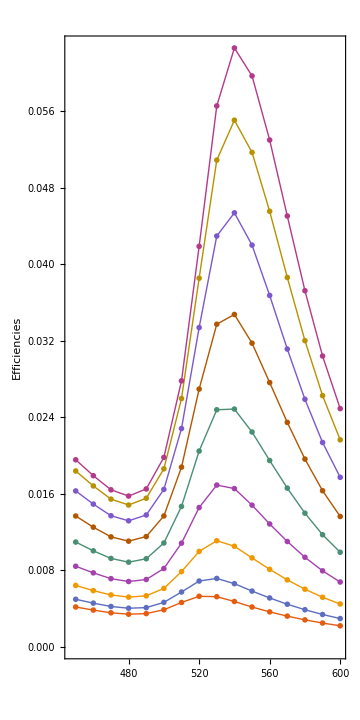
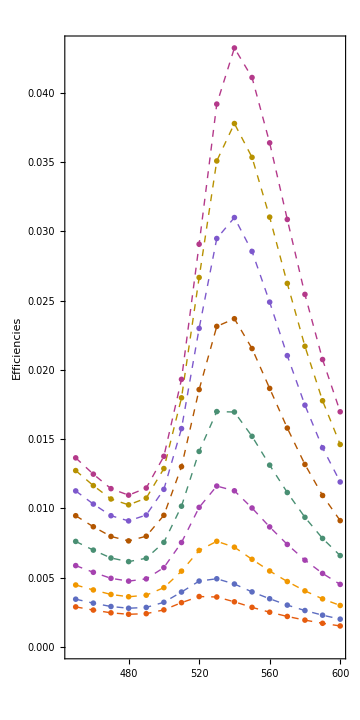
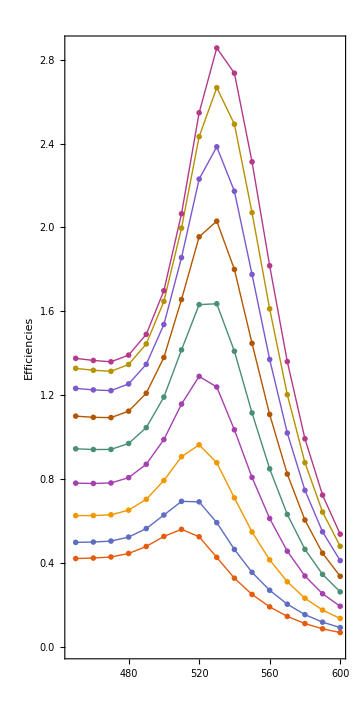
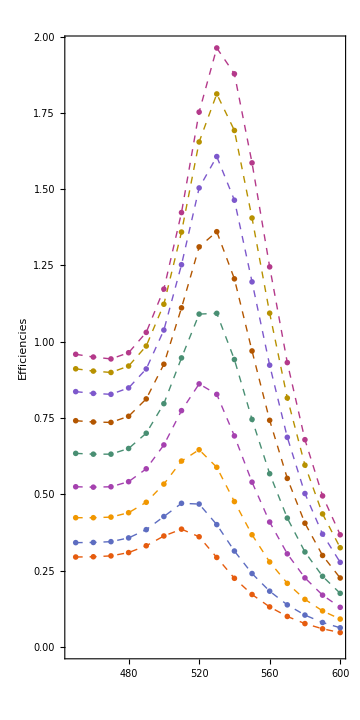
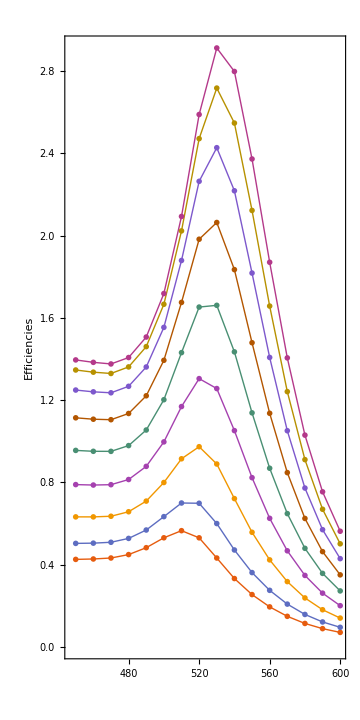
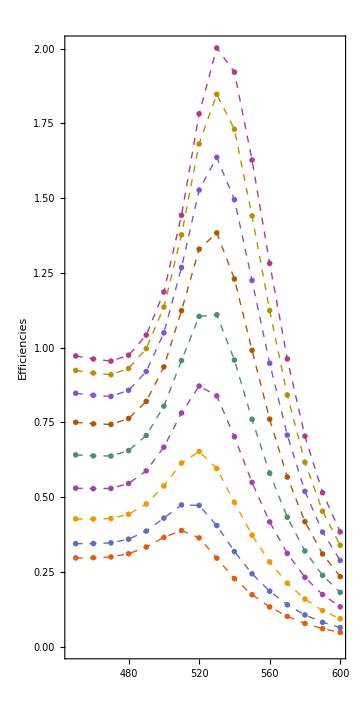

```mathematica
Table[{ListLinePlot[#,PlotStyle->Directive[Thick],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->2]&@ (data[[2,;;,{1,#}]]& /@ Range[i,Length[data[[1,1]] ], 3])
,
ListLinePlot[#,PlotStyle->Directive[Thick,Dashed],PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->2,PlotRange->All]&@ Reverse@(data[[1,;;,{1,#}]]& /@Range[i,Length[data[[1,1]] ], 3])
},{i,2,4}];
```

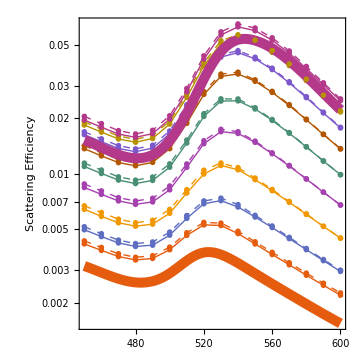
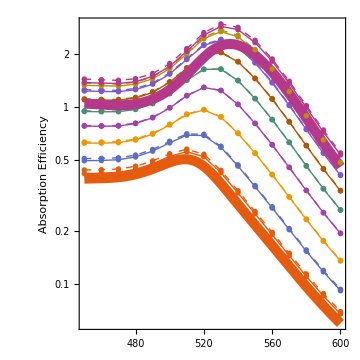
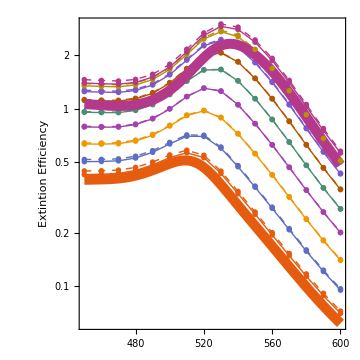

```mathematica
label = #<>"Efficiency"&/@{"Scattering ", "Absorption ", "Extintion "};
algo = Array[{ListLogPlot[fromAir[[#1,#2]]/.{x_,y_}-> {x,1.*y},PlotStyle->Directive[colors[[#2]],Thick],PlotTheme->"Scientific",GridLines-> None,Frame->True, Joined -> True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],label[[#1]]},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->1],
ListLogPlot[fromBK7[[#1,#2]]/.{x_,y_}-> {x,1.5*y},PlotStyle->Directive[colors[[#2]],Thick,Dashed],PlotTheme->"Scientific",GridLines-> None,Frame->True,Joined -> True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],label[[#1]]},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->1,PlotRange->All]}
&,{3,9}];

mie = ListLogPlot[#,Joined -> True,PlotStyle->(Directive[Thickness[.02],#]&/@colors[[{1,9}]])]&/@{sca,abs,ext};

logPlots = Show[Append[algo[[#]],mie[[#]]],PlotRange-> All]&/@Range[3]
(*Export[FileNameJoin[{"Incrusted","logPlot_"<>ToString[#]<>".svg"}],logPlots[[#]]]&/@Range[3]*)
```

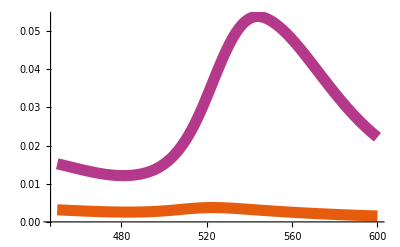
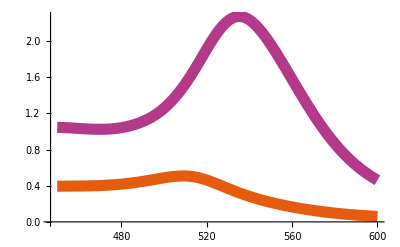
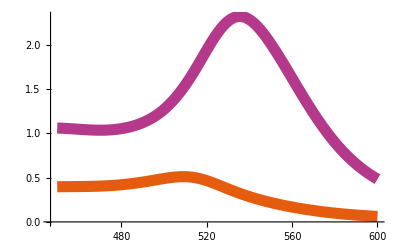

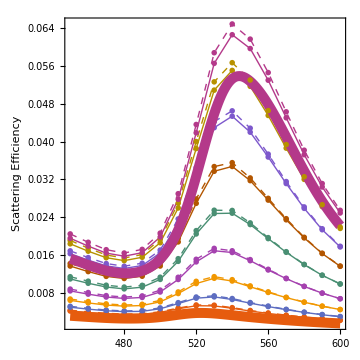
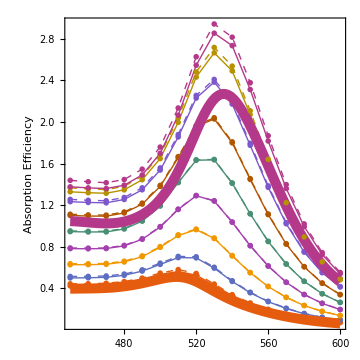
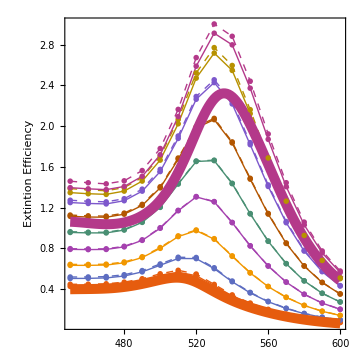

```mathematica
label = #<>"Efficiency"&/@{"Scattering ", "Absorption ", "Extintion "};
algo = Array[{ListPlot[fromAir[[#1,#2]]/.{x_,y_}-> {x,1.*y},PlotStyle->Directive[colors[[#2]],Thick],PlotTheme->"Scientific",GridLines-> None,Frame->True, Joined -> True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],label[[#1]]},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->1],
ListPlot[fromBK7[[#1,#2]]/.{x_,y_}-> {x,1.5*y},PlotStyle->Directive[colors[[#2]],Thick,Dashed],PlotTheme->"Scientific",GridLines-> None,Frame->True,Joined -> True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],label[[#1]]},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->1,PlotRange->All]}
&,{3,9}];

mie = ListPlot[#,Joined -> True,PlotStyle->(Directive[Thickness[.02],#]&/@colors[[{1,9}]])]&/@{sca,abs,ext}

regularPlots = Show[Append[algo[[#]],mie[[#]]],PlotRange-> All]&/@Range[3]

(*Export[FileNameJoin[{"Incrusted","regPlot_"<>ToString[#]<>".svg"}],regularPlots[[#]]]&/@Range[3]*)
```

```mathematica
Export[FileNameJoin[{"Incrusted","plots.svg"}],Grid[{regularPlots,logPlots}]]
```

Incrusted/plots.svg

#### Graphs Effective Ref index

```mathematica
maximos = Table[{ref,grMax[extQ[{ref,nAuSize[#,12.5]},#,12.5]&,{480,550}]},{ref,1,1.5,.01}];
mExt = maximos /.{n_,λ_}-> {n,λ,(Sqrt[n]-1)/(Sqrt[1.5]-1),1-2*(Sqrt[n]-1)/(Sqrt[1.5]-1)};

maximos= Table[{ref,grMax[scaQ[{ref,nAuSize[#,12.5]},#,12.5]&,{480,550}]},{ref,1,1.5,.01}];
mSca = maximos /.{n_,λ_}-> {n,λ,(Sqrt[n]-1)/(Sqrt[1.5]-1),1-2*(Sqrt[n]-1)/(Sqrt[1.5]-1)};

nExt = mExt[[;;,{-1,1}]];
nExtFunc =Interpolation[%]
λExt = mExt[[;;,{-1,2}]];
λExtFunc = Interpolation[%]

nSca= mSca[[;;,{-1,1}]];
nScaFunc=Interpolation[%]
λSca = mSca[[;;,{-1,2}]];
λScaFunc = Interpolation[%]
```

InterpolatingFunction[…]

InterpolatingFunction[…]

InterpolatingFunction[…]

«1 more identical outputs»

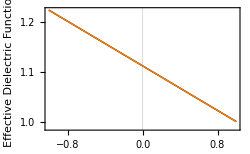

Incrusted/fit.svg

```mathematica
fitPlot  = ListLinePlot[{nSca/.{x_,y_}-> {x,Sqrt[y]},nExt/.{x_,y_}-> {x,Sqrt[y]}},PlotStyle->{Directive[Thick,Black],Directive[Thick,Orange]},PlotTheme-> "Scientific",FrameStyle->Black,ImageSize->250,
FrameLabel->{Style["h/a",texStyle,Italic],Style["Effective Dielectric Function",texStyle]},PlotLegends->Placed[
LineLegend[Automatic,Style[#,texStyle]&/@{"Scattering","Extintion"},LegendLabel->MaTeX["\\varepsilon_{eff}^{\\text{Mie}}"]],{Right,Top}]]
Export[FileNameJoin[{"Incrusted","fit.svg"}],%]
```

```mathematica
(*sca = Table[{λ,scaQ[{nScaFunc[ha],nAuSize[λ,12.5]},λ,12.5]},{ha,1,-1,-.25},{λ, 450,600}];
ext = Table[{λ,extQ[{nScaFunc[ha],nAuSize[λ,12.5]},λ,12.5]},{ha,1,-1,-.25},{λ, 450,600}];
abs = Transpose[{ext[[1,;;,1]],#}]&/@( ext[[;;,;;,2]]-sca[[;;,;;,2]]);
*)
sca = Table[{λ,scaQ[{nScaFunc[ha],nAuSize[λ,12.5]},λ,12.5]},{ha,1,-1,-.25},{λ, 450,600}];
ext = Table[{λ,extQ[{nScaFunc[ha],nAuSize[λ,12.5]},λ,12.5]},{ha,1,-1,-.25},{λ, 450,600}];
abs = Transpose[{ext[[1,;;,1]],#}]&/@( ext[[;;,;;,2]]-sca[[;;,;;,2]]);
```

{{{1.,524.135},{0.75,528.222},{0.5,530.546},{0.25,533.05},{0.,534.993},{-0.25,537.01},{-0.5,538.811},{-0.75,540.},{-1.,540.798}},{{1.,510.},{0.75,515.002},{0.5,520.},{0.25,522.161},{0.,525.419},{-0.25,528.022},{-0.5,530.},{-0.75,530.266},{-1.,531.966}}}

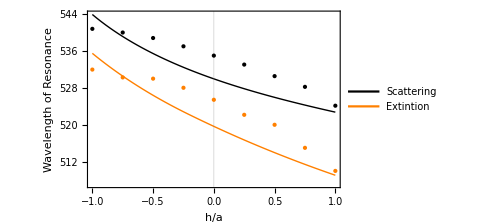

Incrusted/maxFit.svg

```mathematica
algo2 = Transpose@Table[
intS = Interpolation[fromAir[[1,i]]];
intE = Interpolation[fromAir[[3,i]]];
{{1.25-i*.25, grMax[intS,{480,550}]},{1.25-i*.25, grMax[intE,{480,550}]}},{i,9}]


Show[{ListLinePlot[{λSca,λExt},PlotStyle->{Directive[Thick,Black],Directive[Thick,Orange]},PlotTheme-> "Scientific",FrameStyle->Black,ImageSize->Medium,
FrameLabel->{Style["h/a",texStyle,Italic],Style["Wavelength of Resonance",texStyle]},PlotLegends->Placed[
LineLegend[Automatic,Style[#,texStyle]&/@{"Scattering","Extintion"}],{Left,Bottom}]],
ListPlot[algo2,PlotStyle->{Directive[Black,PointSize[Medium]],Directive[Orange,PointSize[Medium]]}]}]
Export[FileNameJoin[{"Incrusted","maxFit.svg"}],%]
```

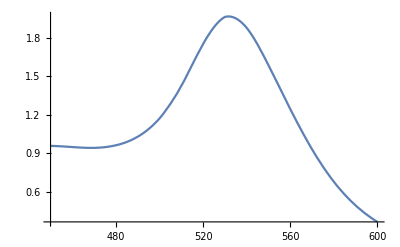

```mathematica
Plot[int[x],{x,450,600}]
```

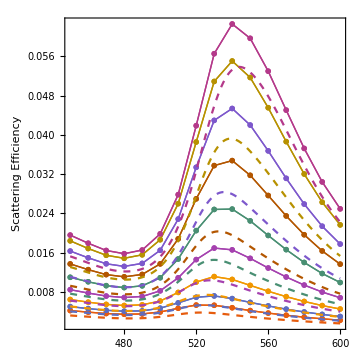
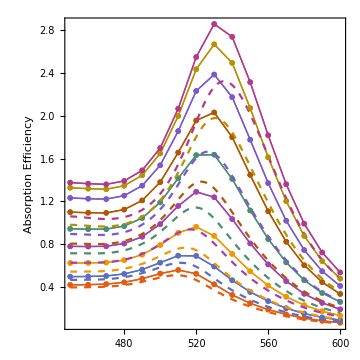
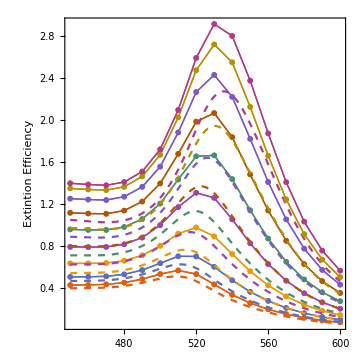

{Incrusted/Mie_FEM1.svg,Incrusted/Mie_FEM2.svg,Incrusted/Mie_FEM3.svg}

```mathematica
label = #<>"Efficiency"&/@{"Scattering ", "Absorption ", "Extintion "};
algo = Array[ListPlot[fromAir[[#1,#2]]/.{x_,y_}-> {x,1.*y},PlotStyle->Directive[colors[[#2]],Thick],PlotTheme->"Scientific",GridLines-> None,Frame->True, Joined -> True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],label[[#1]]},PlotMarkers->{"OpenMarkers",5},
ImageSize-> Medium,AspectRatio->1]
&,{3,9}];

eff = Array[ ListPlot[{sca,ext,abs}[[#1,#2]],PlotStyle->(Directive[Dashed,colors[[#2]]]),Joined->True]&,{3,9}];

Show/@ MapThread[ Show[{#1,#2,#3},PlotRange-> All,AspectRatio-> 1]&,{algo,algo,eff},2]
Export[FileNameJoin[{"Incrusted","Mie_FEM"<>ToString[#]<>".svg"}],%[[#]]]&/@Range[3]
```

# Silicon NP

## Silicon NP 90nm

```mathematica
FileNames["*.csv","Silicon"];
data= Drop[Import[#,"Data"],5]&/@%;
TableForm[%%]
rad = 90(*nm*);
```

Silicon/Si_90nmMie.csv

### Convergencia

```mathematica
mieFem = data[[1,;;,{2,#}]]&/@{3,4,5};
```

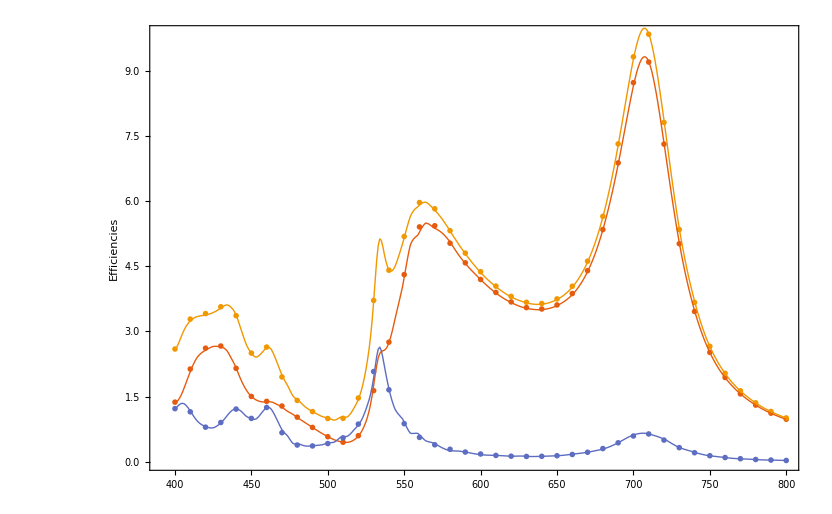

Silicon/Mie-FEM_Air.pdf

```mathematica
amp =1;
(*sca, abs, ext*)
order = {1,2,3};
scadata  = 1;

{scaMie,extMie} = Transpose[Table[Through[{scaQ,extQ}[{1.,nSiFunc[λ]},λ,rad]],{λ, 400,800}]];
Show[{ListPlot[If[#==scadata,mieFem[[#]]/.{x_,y_}-> {x,amp*y},mieFem[[#]]]&/@order,PlotStyle->Thick,PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},
PlotLegends->Placed[SwatchLegend[Automatic,MaTeX[{"Q_{sca}","Q_{abs}","Q_{ext}"},ContentPadding->False],LegendLayout->"Row",
				LegendLabel->LineLegend[{Black,Black},Style[#,texStyle]&/@{"Mie","FEM"},LegendLayout->"Row",LegendMarkers->{None,Graphics[Circle[]]},
						LegendLabel->Style["90 nm-SiNP@Air",texStyle]
						]],{Left,Top}]
,ImageSize-> Medium],
ListLinePlot[{scaMie*amp,extMie-scaMie,extMie},DataRange->{400,800},PlotStyle->Directive[Thick],PlotTheme-> "Scientific"]}]
Export[FileNameJoin[{"Silicon","Mie-FEM_Air.pdf"}],%]
```

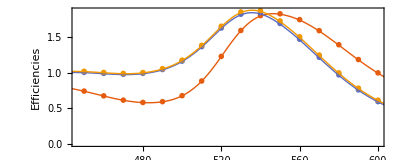

SupportedNP/Mie-FEM_BK7.pdf

```mathematica
amp =50;
(*sca, abs, ext*)
order = {1,2,3};
scadata  = 1;

{scaSize,extSize} = Transpose[Table[Through[{scaQ,extQ}[{1.5,nAuSize[λ,5]},λ,rad]],{λ, 400,800}]];
Show[{ListPlot[If[#==scadata,miebk7[[#]]/.{x_,y_}-> {x,amp*y/1.5},miebk7[[#]]/.{x_,y_}-> {x,y/1.5}]&/@order,PlotStyle->Thick,PlotTheme->"Scientific",GridLines-> None,Frame->True,FrameStyle->Directive[FontFamily->"Latin Modern Roman",FontSize->fs,Black],FrameLabel->{MaTeX["\\lambda\\text{ [nm]}",FontSize->fs,ContentPadding->False],"Efficiencies"},PlotMarkers->{"OpenMarkers",5},
PlotLegends->Placed[SwatchLegend[Automatic,MaTeX[{"Q_{sca}\\times"<>ToString[amp],"Q_{abs}","Q_{ext}"},ContentPadding->False],LegendLayout->"Row",
				LegendLabel->LineLegend[{Black,Black},Style[#,texStyle]&/@{"Mie","FEM"},LegendLayout->"Row",LegendMarkers->{None,Graphics[Circle[]]},
						LegendLabel->Style["12.5 nm-AuNP@BK7",texStyle]
						]],{Right,Bottom}]
,ImageSize-> 400,AspectRatio->1/2.5],
ListLinePlot[{scaSize*amp,extSize-scaSize,extSize},DataRange->{400,800},PlotStyle->Directive[Thick],PlotTheme-> "Scientific"]}]
Export[FileNameJoin[{"SupportedNP","Mie-FEM_BK7.pdf"}],%]
```